```mathematica
$HistoryLength = 0; 
ClearAll["`*"]; 
SetDirectory[NotebookDirectory[]]; 
PacletDirectoryLoad[Directory[]]; 
Get["KirillBelov`WolframWebServer`"];
```

```mathematica
server = CreateWebServer[8080];
```

```mathematica
hello[] := "Hello, World!"
```

```mathematica
plot[func_String, from_?NumericQ, to_?NumericQ] := plot[func, from, to] = 
Plot[Evaluate[Symbol[func][x]], {x, from, to}, ImageSize->Medium];
```

```mathematica
Global`chat`completions[role_String, text_String] := 
WolframAlpha[text, "SpokenResult"]
```

```mathematica
AbsoluteTiming[ExportString[Plot[Sin[x], {x, 10, 20}], "SVG"];]
```

{0.26631,Null}

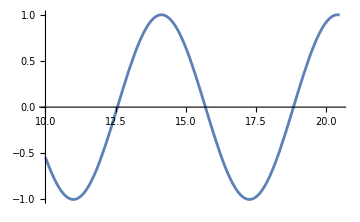
{HoldPattern[plot[Sin,10,20.5]]:>-Graphics-,HoldPattern[plot[func_String,from_?NumericQ,to_?NumericQ]]:>(plot[func,from,to]=Plot[Evaluate[Symbol[func][x]],{x,from,to},ImageSize→Medium])}

```mathematica
DownValues[plot]
```